```mathematica
datafile=FileNameJoin[{NotebookDirectory[],"obs_data_w.xlsx"}];
```

```mathematica
trainingdatasetnb = Import[datafile][[1]];
```

```mathematica
trainingdatasetnb =Drop[ trainingdatasetnb,1];
```

```mathematica
trainingdatalengthnb = Length[trainingdatasetnb];
```

```mathematica
Voltage = {};
CurrentDensity= {};
Temparature = {};
Uncertanity= {};
```

```mathematica
c1 = 0;
While[(c1 += 1) <trainingdatalengthnb ,
  {
    
    Voltage = Append[Voltage, trainingdatasetnb[[c1]][[2]]];
    Temparature = Append[Temparature, trainingdatasetnb[[c1]][[3]]];
    Uncertanity = Append[Uncertanity, trainingdatasetnb[[c1]][[4]]];
    CurrentDensity = Append[CurrentDensity, trainingdatasetnb[[c1]][[5]]];
    };
  ];
```

```mathematica
inputset= Transpose[{Temparature,CurrentDensity}];
```

```mathematica
trainingset= {};
For[i=1,i<trainingdatalengthnb,i++,trainingset = Append[trainingset,inputset[[i]] -> Voltage[[i]]]]
```

```mathematica
LinearPrediction= Predict[trainingset,Method->"LinearRegression"];
infolinearreg = PredictorInformation[LinearPrediction]
NeuralNetwordPrediction = Predict[trainingset,Method->"NeuralNetwork"];		
infoNeuralNetwork = PredictorInformation[NeuralNetwordPrediction];
NearestNeighborPrediction= Predict[trainingset,Method->"NearestNeighbors"];	
infoNN = PredictorInformation[NearestNeighborPrediction];
RandomForestPrediction= Predict[trainingset,Method->"RandomForest"];
infoRF = PredictorInformation[RandomForestPrediction];
```

Predictor information
Input type | NumericalVector (length: 2)
Method | LinearRegression
Standard deviation | 0.983 ± 0.012
Loss | 1.4 ± 0.012
Single evaluation time | QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[MachineLearning`file131General`PackagePrivate`iHumanReadableQuantity[QuantityUnit[UnitConvert[QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[0.0011,Seconds]]]],QuantityMagnitude[UnitConvert[QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[0.0011,Seconds]]]]],1/Examples]]
Batch evaluation speed | QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[MachineLearning`file131General`PackagePrivate`iHumanReadableQuantity[QuantityUnit[UnitConvert[QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[430000.,1/Seconds]]]],QuantityMagnitude[UnitConvert[QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[430000.,1/Seconds]]]]],Examples]]
Predictor memory | MachineLearning`file131General`PackagePrivate`iHumanReadableQuantity[QuantityUnit[UnitConvert[QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[335904,Bytes]]]],QuantityMagnitude[UnitConvert[QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[335904,Bytes]]]]]
Training examples used | QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[7893,Examples]]
Training time | MachineLearning`file131General`PackagePrivate`iHumanReadableQuantity[QuantityUnit[UnitConvert[QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[3.87316,Seconds]]]],QuantityMagnitude[UnitConvert[QuantityUnits`Private`ToQuantity[QuantityUnits`Private`UnknownQuantity[3.87316,Seconds]]]]]
 |

```mathematica
Voltagetobeplotted = {};
Currenttobeplotted = {};
Temparaturetobeplotted = {};
```

```mathematica
c1 = 0;
While[(c1 += 1) <77,
  {
    
    Voltagetobeplotted = Append[Voltagetobeplotted, Voltage[[c1]]];
    Currenttobeplotted = Append[Currenttobeplotted, CurrentDensity[[c1]]];
Temparaturetobeplotted = Append[Temparaturetobeplotted, Temparature[[c1]]];
    };
  ];
```

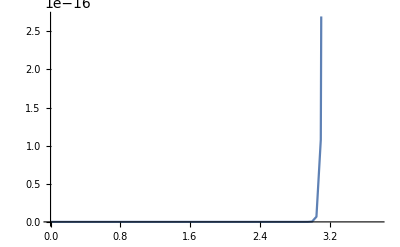

```mathematica
toplotiv = Transpose[{Voltagetobeplotted,Currenttobeplotted}];
OutputValueplot =ListLinePlot[toplotiv,PlotRange->Automatic,PlotRange->{0,1}]
```

```mathematica
DesiredConditions = {140,0.1};	
PredictedVonbyRFMethod = RandomForestPrediction[DesiredConditions]
```

3.54618